```mathematica
vx0=4; vy0=4;
A=0.5;
g=9.8;
w=0.3;
border[x_]:=A*Sin[w*x];
```

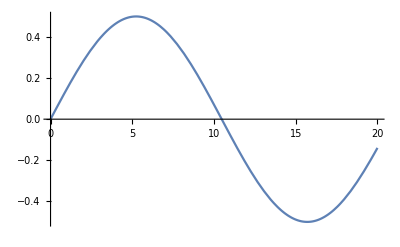

```mathematica
Plot[border[x],{x,0,20}]
```

```mathematica
n=5000; dx=0.001;
x=0; y=0;
xyVector={{x,y}};
vxVector={};
vyVector={};
vx=vx0; vy=vy0;
For[i=0,i≤n,i++,
vxTMP=vx;
vyTMP=vy-g*dx;
xTMP=x+vxTMP*dx;
yTMP=y+vyTMP*dx;
If[border[xTMP]>yTMP,vyTMP=-vyTMP];
x=xTMP;
y=yTMP;
vx=vxTMP;
vy=vyTMP;
AppendTo[xyVector,{x,y}]]
```

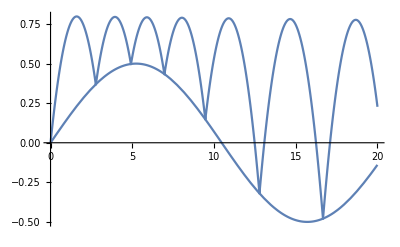

```mathematica
Show[Plot[border[x],{x,0,20}],ListLinePlot[xyVector],PlotRange->All]
```